## Modelo contínuo do sistema sem zeros

```mathematica
As = {{-3588,-4.506*10^4,0},{1,0,0},{0,1,0}}
```

{{-3588,-45060.,0},{1,0,0},{0,1,0}}

```mathematica
Bs = {{2.899*10^7},{0},{0}}
```

{{2.899×10^7},{0},{0}}

```mathematica
Cs = {{0,1,0}}
```

{{0,1,0}}

```mathematica
Ds = {{0}}
```

{{0}}

```mathematica
ss = StateSpaceModel[{As,Bs,Cs,Ds}]
```

(-3588 | -45060. | 0 | 2.899×10^7
1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 1 | 0 | 0)_^𝒮

## Modelo discreto do sistema

Não tenho certeza de qual método utilizar para discretizar o sistema. Inicialmente utilizarei o FRR.

```mathematica
SSd = FullSimplify[ToDiscreteTimeModel[ss,Ts,Method->"ForwardRectangularRule"]]
```

(1-3588 Ts | -45060. Ts | 0 | 2.899×10^7 Ts
Ts | 1 | 0 | 0
0 | Ts | 1 | 0
0 | 1 | 0 | 0)_Ts^𝒮

## Analisando a estabilidade do sistema

```mathematica
roots = Solve[TransferFunctionModel[SSd][[1]][[2]]==0,z ]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{z→1.},{z→1.-3575.4 Ts},{z→1.-12.6028 Ts}}

### Primeiro pólo do sistema em função do sampling time

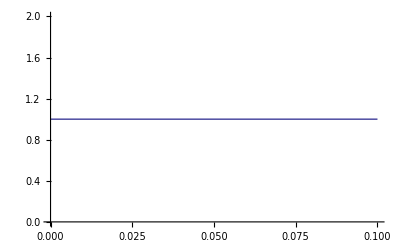

```mathematica
Plot[z/.(roots)[[1]],{Ts,0,0.1}]
```

### Segundo pólo do sistema em função do sampling time

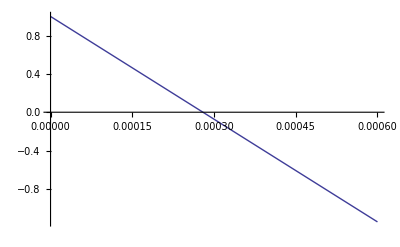

```mathematica
Plot[z/.(roots)[[2]],{Ts,0.00,0.0006}]
```

### Terceiro pólo do sistema em função do sampling time

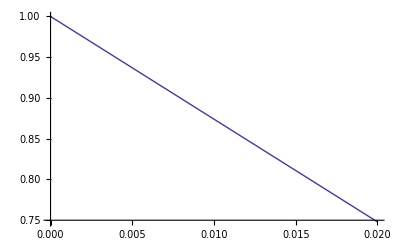

```mathematica
Plot[z/.(roots)[[3]],{Ts,0.00,0.02}]
```